```mathematica
f[x_,h_,r_]:=h+r x−x^2
fDot[x_,r_]:=r -2x
Solve[fDot[x,r] ==0,x]
```

{{x→r/2}}

```mathematica
f[r/2,h,r]
Solve[f[r/2,h,r]==0,h]
```

```mathematica
h+r^2/4
```

h+r^2/4

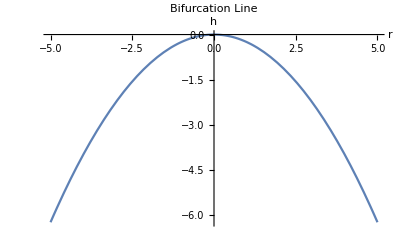

/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/h_r_phase.png

```mathematica
g=Plot[-r^2/4,{r,-5,5},AxesLabel->{"r","h"}, PlotLabel->"Bifurcation Line"]
Export["/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/h_r_phase.png",g,"PNG", ImageSize->{1500}]
```

```mathematica
Solve[f[x,h,r] ==0,x]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
xRoot1 [h,r] := 1/2 (r-√(4 h+r^2))
xRoot2[h,r]:= 1/2 (r+√(4 h+r^2))
scale = 10;
g = Plot3D[{xRoot1[h,r],xRoot2[h,r]},{h,-scale,scale},{r,-scale,scale},AxesLabel->{"h","r", "x"},PlotLabel->"Fixed Point Surface"] 
Export["/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/surf_plot.png",g,"PNG", ImageSize->{1500}]
```

-Graphics3D-

/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/surf_plot.png